```mathematica
(*Final*)
```

```mathematica
(* ---------------- vars ----------------*)
nVars=0;
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
qs={};
qsvars={};
qsInit={};
dqsInit={};
(* ------------ objects ----------------- *)
nObjects=0;
objNames={};
(* Properties *)
masses={};
inertias={};
lens={};
g=5;
(* Transformation matrices *)
Ts={};
pFronts={};
pBacks={};

(* Vertices for impact detection *)
impObjVertexs={};
impObjVertexGroupIDs={};
(* Edges for impact detection *)
impObjEdges={};
impObjEdgeGroupIDs={};


(* Funcs for creating objects *)
CreateLink[linkgeometry_]:=Module[{l,T,pFront,pBack},
nObjects=nObjects+1;
{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];
pushLensMassInertia[l];

(*Vars*)
nDOF=3;
{objqs,objqsvars}=pushVars[nDOF];
xvar=objqs[[1]];
yvar=objqs[[2]];
θvar=objqs[[3]];
{T,pFront,pBack,TFront,TBack}=CalcAndPushT[xvar,yvar,θvar,l];

objqsinit={(p1x+p2x)/2,(p1y+p2y)/2,myArcTan[p1x,p1y,p2x,p2y]};
qsInit=Join[qsInit,objqsinit];
dqsInit=Join[dqsInit,Table[RandomReal[]*initRandVelocity,{i,1,nDOF}]];

(*Push vertices and edge for impact*)
PushVertex[pFront,nthGroup];
PushVertex[pBack,nthGroup];
PushEdge[{pFront[[1;;2,1]],pBack[[1;;2,1]]},nthGroup];
{T,pFront,pBack,TFront,TBack}(*Return*)
];

AppendLink[T0_,θ0_,l_]:=Module[{T,pFront,pBack,x,y},
nObjects=nObjects+1;
pushLensMassInertia[l];

(*Vars*)
nDOF=1;
{objqs,objqsvars}=pushVars[nDOF];
θvar=objqs[[1]];

T=FullSimplify[T0.Rotz4[θvar].Trans4[l/2,0],qs∈Reals];
{pFront,pBack,TFront,TBack}=pushPEnds[T,l];
pushT[T];

qsInit=Append[qsInit,θ0];
dqsInit=Append[dqsInit,RandomReal[]*initRandVelocity];

(*Impact*)
PushVertex[pFront,nthGroup];
PushEdge[{pFront[[1;;2,1]],pBack[[1;;2,1]]},nthGroup];
{T,pFront,pBack,TFront,TBack}(*Return*)
];

CreateWall[linkgeometry_]:=Module[{l,T,pFront,pBack},
nObjects=nObjects+1;
{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];
pushLensMassInertia[l];

x=(p1x+p2x)/2;
y=(p1y+p2y)/2;
θ=myArcTan[p1x,p1y,p2x,p2y];
{T,pFront,pBack,TFront,TBack}=CalcAndPushT[x,y,θ,l];

PushVertex[pFront,nthGroup];
PushVertex[pBack,nthGroup];
PushEdge[linkgeometry,nthGroup];
{T,pFront,pBack,TFront,TBack}(*Return*)
];

(* ------------------------------------------------------------------------;-------------------------- Create objects here ---------------------------;---------------------------------------------------------------- *)
CreateObjects[];
```

```mathematica
(* Remove duplicated vertices *)
n=Length[impObjVertexs];
tmpimpObjVertexs={};
tmpimpObjVertexGroupIDs={};
For[i=1,i≤n,i=i+1,
ifDup=False;
x0=impObjVertexs[[i,1,1]];
y0=impObjVertexs[[i,2,1]];
For[j=1,j≤Length[tmpimpObjVertexs],j=j+1,
If[tmpimpObjVertexs[[j,1,1]]==x0 &&tmpimpObjVertexs[[j,2,1]]==y0,
ifDup=True;
Break[]
]];
If[ifDup==False,
AppendTo[tmpimpObjVertexs,impObjVertexs[[i]]];
AppendTo[tmpimpObjVertexGroupIDs,impObjVertexGroupIDs[[i]]]
];
];
impObjVertexs=tmpimpObjVertexs;
impObjVertexGroupIDs=tmpimpObjVertexGroupIDs;
```

```mathematica
(* Prepare *)
dqs=D[qs,t];
ddqs=D[dqs,t];
```

```mathematica
(* --------------- Left side of EL eqs -------------- *)
(* Body generalized mass, composed of Inertia Tensor and Mass Matrix *)
getGb[j_,m_]:=ArrayFlatten[({{DiagonalMatrix[{j,j,j}], Zeros[3,3]}, {Zeros[3,3], DiagonalMatrix[{m,m,m}]}})]
Gbs=Table[getGb[inertias[[i]],masses[[i]]],{i,1,nObjects}]//Simplify;
(* Body screw axis *)
Vbs=Table[GenUnhat[InvT[Ts[[i]]].D[Ts[[i]],t]],{i,1,nObjects}]//Simplify;
(* Lagrange Equations: Kinetic and Potential Energy *)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
KEs=Table[GetKE[Gbs[[i]],Vbs[[i]]],{i,1,nObjects}]//Simplify;
PEs=Table[GetPE[masses[[i]],Ts[[i]]],{i,1,nObjects}]//Simplify;
Lag=Simplify[Total[Join[KEs,-PEs]],qs∈Reals];
(* Left side of Euler-Lagrange Equations*)
ELeqsLeft=Simplify[D[D[Lag,{dqs}],t]-D[Lag,{qs}],qs∈Reals];
```

```mathematica
(* --------------- Right side of EL eqs -------------- *)
(* Constraints *)
(*
conslink1P1x=p1Ends[[1]][[2,1]];(* y=0 *)
conslink1P1y=p1Ends[[2]][[2,1]];(* y=0 *)
*)
nCons=Length[cons];
If[nCons>0,
(λs=Transpose[{Table[Symbol["$λ"<>ToString@i],{i,nCons}]}];
consgrad=Transpose[Grad[cons,qs]]; (* Grad[2,5]->Mat(2,5),Transpose->(5,2)*)
consddt=Simplify[D[D[cons,t],t],qs∈Reals];)];
```

```mathematica
(* External forces *)
externalForces=ConstantArray[0,nVars];
```

```mathematica
(* ----------------------------- *)
(* Solve *)
If[nCons>0,(* with constraints *)
(EulerLagEqs=Thread[ELeqsLeft==Flatten[consgrad.λs]+externalForces]//Simplify;
consddtEqs=TurnToEq[consddt,ConstantArray[0,nCons]];
EQ=Solve[Join[EulerLagEqs,consddtEqs],Join[ddqs,Flatten[λs]]]),
(* No constraint *)
EulerLagEqs=Simplify[TurnToEq[ELeqsLeft,externalForces],qs∈Reals];
EQ=Solve[EulerLagEqs,ddqs]];
```

```mathematica
(* ----------------------------- *)
(* Preprae for NDSolve *)
timeend=10;
MAXIMPACTTIMES=100;
impactDetectionError=0.1;
intergrationMaxStepSize=0.01;
ifprint=False;

SetUpImpacts[]
ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];
```

```mathematica
(* NDsolve *)
{end,data,bounces}=BouncingBall[qsInit,dqsInit];
```

Computing simulation: 2.16976 / 10 ...

Computing simulation: 4.28534 / 10 ...

Computing simulation: 6.2262 / 10 ...

Computing simulation: 8.10347 / 10 ...

Computing simulation is completed.

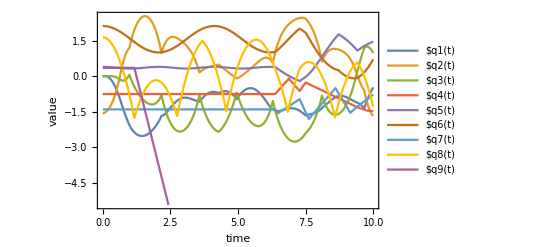

```mathematica
(* Plot *)
qsPlot=Table[Piecewise[qsvars[[i]]/.data],{i,1,nVars}];
Show[Plot[Evaluate[qsPlot],{t,0,end},PlotLegends->qs,
	PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}]]
```

```mathematica
plotGetLinkCoords[T_,l_]:=Module[{pFront,pBack},
p0x=T[[1,4]];
p0y=T[[2,4]];
pFront=T.Transpose[{{l/2,0,0,1}}]//Simplify;
pBack=T.Transpose[{{-l/2,0,0,1}}]//Simplify;
Line[{pFront[[1;;2,1]],pBack[[1;;2,1]]}]
]
links=Table[plotGetLinkCoords[Ts[[i]],lens[[i]]],{i,1,nObjects}];
```

```mathematica
(* Animate *)
(*linksCoords[i_]:=(links[[i]]/.sim)[[1]];*)
linksCoords[j_]:=links[[j]]/.Table[qs[[i]]->qsPlot[[i]],{i,1,nVars}];
LinksForAnimation[tt_]:=(Table[linksCoords[i],{i,1,Length[links]}])/.t->tt;
Animate[Show[
{Graphics[{Thickness[impactDetectionError/8],LinksForAnimation[t]}]
},PlotRange-> {{-3,3},{-3,3}},Frame-> True],{t,0,timeend},AnimationRate->1]
```